```mathematica
Solve[DSolve[{u'[t]== (2890.9-29.21*u[t]^2)/2507.27, u[0]== 0},u[t],t][[1]]== 9.8489,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{u[t]→(9.94834 (-1.+1. ⅇ^(0.231799 t)))/(1.+1. ⅇ^(0.231799 t))}==9.8489,t]

```mathematica
Solve[(9.948343127503204 (-1.+1. ⅇ^(0.2317988112603498 t)))/(1.+1. ⅇ^(0.2317988112603498 t))== 9.8489,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→22.8375}}

```mathematica
∫_0^9.8489 (2507.27/(2890.9-29.2*u^2))ⅆu
```

22.7685

```mathematica
a = 20306.7
b=17658
Q=10
∫_0.5^5 (a*(Q/(2*π*r))+b*(Q/(2*π*r))^2)ⅆr
```

20306.7

17658

10

154928.

```mathematica
Clear[Q,d,ϵ]

ρ=62.3
x=Q/(2π*r)
μ=0.000672
ode= (1.75*ρ*x^2(1-ϵ))/(d*ϵ)+(150*(1-ϵ)^2*μ*x)/(d*ϵ^3)
Δp = ∫_0.25^25 odeⅆr
```

62.3

Q/(2 π r)

0.000672

(0.0160428 Q (1-ϵ)^2)/(d r ϵ^3)+(2.76164 Q^2 (1-ϵ))/(d r^2 ϵ)

(Q (0.0738799-0.14776 ϵ+(0.0738799+10.9361 Q) ϵ^2-10.9361 Q ϵ^3))/(d ϵ^3)

```mathematica
f[Q_]:= (Q (0.073879908367046-0.147759816734092 ϵ+(0.073879908367046+10.936076626139705 Q) ϵ^2-10.936076626139705 Q ϵ^3))/(d ϵ^3)

NSolve[{f[100]== 20,f[200]== 50},{ϵ,d},Reals]

f[100]
f[200]
```

{{ϵ→-0.00475666,d→-4.62009×10^6},{d→4.59822×10^6,ϵ→0.00473414}}

(100 (0.0738799-0.14776 ϵ+1093.68 ϵ^2-1093.61 ϵ^3))/(d ϵ^3)

(200 (0.0738799-0.14776 ϵ+2187.29 ϵ^2-2187.22 ϵ^3))/(d ϵ^3)

```mathematica
f[Q_,d_, ϵ_]:= (Q (0.073879908367046-0.147759816734092 ϵ+(0.073879908367046+10.936076626139705 Q) ϵ^2-10.936076626139705 Q ϵ^3))/(d ϵ^3)
f[300, 4.59822*10^6,0.00473414]
```

90.

```mathematica
g[Q_, d_, ϵ_] := (Q (0.011120034247693322-0.022240068495386643 ϵ+(0.011120034247693322+5.523271023302772 Q) ϵ^2-5.523271023302772 Q ϵ^3))/(d ϵ^3)
g[100, 4.59822*10^6,0.00473414]
```

4.78298

```mathematica
Solve[(150*0.000672*(1-0.42)^2*u)/(62.3*0.4167^2*0.42^2)+(1.75*u^2*(1-0.42))/((0.4167)*(0.42)^3)== 32.2*0.03, u]
```

{{u→-0.171682},{u→0.171142}}

```mathematica
Solve[(24*μ)/(ρ*u*Di)== (F/((p*Di^2)/4))/(0.5*ρ*u^2),F]
```

{{F→3. Di p u μ}}

```mathematica
Simplify[DSolve[{h'[t]== g-c*h[t]^2, h[0]==0},h[t],t]]
Clear[g]
```

```mathematica
{{h[t]->(√g Tanh[√c √g t])/(√c)}}
```

```mathematica
(Exp[(Sqrt[g*c])*2t]-1)/(Exp[(Sqrt[g*c])*2t]+1)//StandardForm
```

(-1+ⅇ^(2 √(c g) t))/(1+ⅇ^(2 √(c g) t))

```mathematica
Simplify[Solve[t== 1/(2*Sqrt[g*c])*Log[(Sqrt[g]+u*Sqrt[c])/(Sqrt[g]-u*Sqrt[c])],u]]
```

{{u→ConditionalExpression[((-1+ⅇ^(2 √(c g) t)) √g)/(√c (1+ⅇ^(2 √(c g) t))), -π<2 Im[√(c g) t]≤π]}}

1

1

1

«1 more identical outputs»

h'[t]==-2-h[t]^2

{{h[t]→-√2 Tan[√2 t]}}

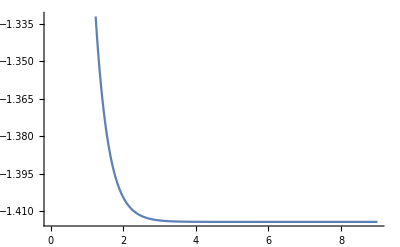

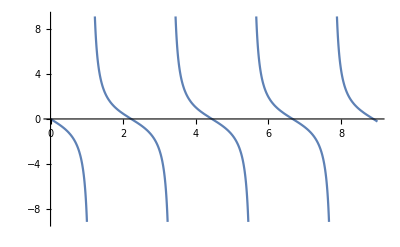

```mathematica
Clear[W,B,Di,M]

W=1
B=1
Di=1
M=1

eqn= h'[t]== (-Di*h[t]^2-W-B)/M
p =DSolve[{eqn, h[0]== 0},h[t],t]
Plot[(√(-B-W) Tan[(√Di t √(-B-W))/M])/(√Di),{t,0,9}]
Plot[-√2 Tan[√2 t],{t,0,9}]
```